```mathematica
SetDirectory[NotebookDirectory[]];
Needs["ErrorBarPlots`"]
SetOptions[ListPlot,Joined->True,Frame->True];
cm=72/2.54;mm=cm/10;
scicol=55;
(*Eric's directories*)
dropboxDir=If[$OperatingSystem=="MacOSX",FileNameJoin[{"/","Users","erictai","Dropbox"}],"D:\\Dropbox"];
repoDir=If[$OperatingSystem=="MacOSX",FileNameJoin[{"/","Users","erictai","RbPapers"}],"D:\\RbPapers"];
outputdir=FileNameJoin[{dropboxDir,"Harvard","mathematica","mbl_figures"}];
(*Robert's directories*)
dropboxDir=If[$OperatingSystem=="MacOSX",FileNameJoin[{"/","Users","erictai","Dropbox"}],"C:\\Users\\Alex\\Dropbox"];
repoDir=If[$OperatingSystem=="MacOSX",FileNameJoin[{"/","Users","erictai","RbPapers"}],"C:\\RbPapers"];
outputdir=NotebookDirectory[];
<<MaTeX`
(*SetOptions[MaTeX,"BasePreamble"->{"\\usepackage{amsmath,amssymb}"}];*)
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color,units,bm,helvet}","\\mathchardef\\mhyphen=\"2D","\\renewcommand{\\familydefault}{\\sfdefault}"}];
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color,units,bm,helvet}","\\definecolor{blue}{rgb}{0.368417,0.506779,0.709798}","\\definecolor{orange}{rgb}{0.880722,0.611041,0.142051}"}];
If[$OperatingSystem=="MacOSX",
ConfigureMaTeX["Ghostscript" -> FileNameJoin[{"/","usr","local","bin","gs"}]],
(*(*Eric's gs*)
ConfigureMaTeX["Ghostscript" -> FileNameJoin[{"C:","Program Files","gs","gs9.19","bin","gswin64c.exe"}]]*)
(*Robert's gs*)
ConfigureMaTeX["Ghostscript" -> FileNameJoin[{"C:","Program Files","gs","gs9.20","bin","gswin64c.exe"}]]]
```

Ghostscript is not found at C:\Program Files\gs\gs9.20\bin\gswin64c.exe

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Ghostscript is not found at C:\Program Files\gs\gs9.20\bin\gswin64c.exe

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

{pdfLaTeX→C:\Program Files (x86)\MiKTeX 2.9\miktex\bin\pdflatex.exe,CacheSize→100,Ghostscript→C:\Program Files\gs\gs9.20\bin\gswin64c.exe}

```mathematica
null=##&[];
datadir=FileNameJoin[{repoDir,"MBL","data_analysis","data_repo"}];
lighten[color_,percentage_:0.5]:=Blend[{White,color},percentage]
stripTickLabels[tks_]:=Transpose[{tks⟦All,1⟧,ConstantArray["",{Length[tks]}],tks⟦All,3⟧}];
Clear[formatText];
formatText[str_,siz_:6]:=Style[str,FontFamily->"Helvetica",FontSize->siz];
```

```mathematica
hatchedRect[mirRadius_,mirThickness_,mirAngle_,dirs_]:=Module[{mirRect,mirGr,linelist,mirHatch,hatchSpec,nHatches},
mirRect={EdgeForm[Directive[Delete[dirs,0]]],FaceForm[],Rectangle[{-mirRadius,-mirThickness},{mirRadius,0}]};
hatchSpec={Delete[dirs,0]};
nHatches=26;
linelist=Table[{{Max[ii,-mirRadius],mirThickness Min[((Max[ii,-mirRadius]-ii)/mirThickness-1),0]},
{Min[ii+mirThickness,mirRadius],mirThickness((Min[ii+mirThickness,mirRadius]-ii)/mirThickness-1)}},{ii,Subdivide[-mirRadius-1,mirRadius-1,nHatches]}];
mirHatch={Delete[hatchSpec,0],Line[linelist⟦2;;⟧]};

mirGr=Rotate[{mirRect,mirHatch},mirAngle,{0,0}];
Return[mirGr]]
Graphics[{hatchedRect[5,5/5,0,{Thickness[0.002],Black}],Disk[{0,0},0.1]}];
```

```mathematica
truncatePts[pts_,targetTime_]:=Module[{ii,set,idx,shortPts},
shortPts=pts;
For[ii=1,ii≤Length[pts],ii++,
set=pts⟦ii,;;,1⟧;
idx=Ordering[Abs[set-targetTime],1]⟦1⟧;
shortPts⟦ii⟧=pts⟦ii,;;idx-1⟧];
Return[shortPts]]
```

## plotting subroutines

```mathematica
plotColorA=ColorData[99,1];
plotColorB=ColorData[99,2];
plotColorC=ColorData[99,4];
plotColorD=ColorData[99,3];
colorPalette={plotColorB,plotColorA,plotColorC,plotColorD};
colorPalette={plotColorB,plotColorA,plotColorD,plotColorC};
colorPalette=ColorData[99,"ColorList"]⟦{2,1,4,3}⟧;
AppendTo[colorPalette,GrayLevel[0.5]]
AppendTo[colorPalette,lighten[colorPalette⟦1⟧,0.65]];
AppendTo[colorPalette,lighten[colorPalette⟦2⟧,0.65]]
Clear[createMkrSpec];
Clear[createLineSpec];
lighten[color_]:=Blend[{White,color},0.5];
(*the following helper functions expect 'dataPts' to be defined. Hence, I recommend that they be placed inside a Block where such things are defined.*)
createMkrSpec[r_,t_,indices_:0]:=Module[{mkrspec},
mkrspec=If[Length[indices]==0,
Map[{Graphics@{#,EdgeForm[Directive[#,Thickness[t]]],White,Disk[]},r}&,colorPalette⟦;;Length[dataPts]⟧],
Map[{Graphics@{#,EdgeForm[Directive[#,Thickness[t]]],White,Disk[]},r}&,colorPalette⟦indices⟧]];
Return[mkrspec]];
createMkrSpec[r_,t_,idx_:0]:=Module[{mkrspec,indices,shapeList,shapeSize},
indices=If[Length[idx]==0,Range[1,Length[dataPts]],idx];
shapeList={Disk[],Polygon[{{0,1},{1,2},{2,1},{1,0}}],Rectangle[]};
shapeSize={1,1.2,1};
mkrspec=ConstantArray[0,{Length[indices]}];
For[ii=1,ii≤Length[mkrspec],ii++,
mkrspec⟦ii⟧={Graphics@{colorPalette⟦indices⟦ii⟧⟧,
EdgeForm[Directive[colorPalette⟦indices⟦ii⟧⟧,Thickness[t/shapeSize⟦Mod[ii,Length[shapeSize],1]⟧]]],
White,
shapeList⟦Mod[ii,Length[shapeList],1]⟧},r shapeSize⟦Mod[ii,Length[shapeSize],1]⟧}];
Return[mkrspec]];
Clear[noCapErrorBarFunction];
noCapErrorBarFunction[t_]:=Module[{},Return[Function[{coords,errs},{Thickness[t],Line[{{coords,coords+{0,errs⟦2,2⟧}},{coords,coords+{0,errs⟦2,1⟧}}}]}]]];
createLineSpec[dirs_,indices_:0]:=Module[{linespec},
linespec=If[Length[indices]==0,
Map[Directive[Delete[Flatten[{dirs,lighten[#]},1],0]]&,colorPalette⟦;;Length[dataPts]⟧],
Map[Directive[Delete[Flatten[{dirs,lighten[#]},1],0]]&,colorPalette⟦indices⟧]];
Return[linespec]];
```

{RGBColor[0.0504678, 0.526626, 0.627561],RGBColor[0.65, 0., 0.],RGBColor[0.435888, 0.259065, 0.71028],RGBColor[0.752461, 0.362306, 0.125339],GrayLevel[0.5]}

{RGBColor[0.0504678, 0.526626, 0.627561],RGBColor[0.65, 0., 0.],RGBColor[0.435888, 0.259065, 0.71028],RGBColor[0.752461, 0.362306, 0.125339],GrayLevel[0.5],RGBColor[0.38280406999999994, 0.6923069, 0.75791465],RGBColor[0.7725, 0.35, 0.35]}

```mathematica
customListPlot[dataPts_,indices_:0]:=Module[{gr},
(*this function expects errBarFunc, mkrRad, mkrTh to be implicitly defined, i.e. use this in a Block statement*)

gr=Show[{ErrorListPlot[dataPts,Joined->False,
PlotMarkers->None,
PlotStyle->If[Length[indices]==0,colorPalette⟦;;Length[dataPts]⟧,colorPalette⟦indices⟧],
ErrorBarFunction->errBarFunc],
ListPlot[dataPts⟦All,All,1⟧,
PlotMarkers->createMkrSpec[mkrRad,mkrTh,indices],
Joined->False]}];
Return[gr]];
```

```mathematica
Clear[customListPlot2];
customListPlot2[theoryPts_,dataPts_,indices_,opts:OptionsPattern[]]:=Module[{gr},
(*this function expects errBarFunc, mkrRad, mkrTh, theoryLineSpec to be implicitly defined, i.e. use this in a Block statement*)

gr=Show[{ListPlot[theoryPts,
AlignmentPoint->Scaled[{0.5,0.5}],
FilterRules[{opts},Options[ListPlot]],
PlotStyle->createLineSpec[theoryLineSpec,indices],
Axes->False,
FrameStyle->Directive[FontSize->6,FontFamily->"Helvetica"],
Joined->True],
ErrorListPlot[dataPts,Joined->False,
PlotMarkers->None,
PlotStyle->If[Length[indices]==0,colorPalette⟦;;Length[dataPts]⟧,colorPalette⟦indices⟧],
ErrorBarFunction->errBarFunc],
ListPlot[dataPts⟦All,All,1⟧,
PlotMarkers->createMkrSpec[mkrRad,mkrTh,indices],
Joined->False]}];
Return[gr]];
```

```mathematica
importFolders[folders_,names_,theorySuffix_,dataSuffix_,datatype_:"linear"]:=Module[{flist,nlist,
prefix,,theory,data,
theoryPts,dataPts},

flist=If[Length[folders]==0,{folders},folders];
nlist=If[Length[names]==0,{names},names];
theoryPts=ConstantArray[0,{Length[flist]}];
dataPts=ConstantArray[0,{Length[flist]}];
For[ii=1,ii≤Length[flist],ii++,
prefix=FileNameJoin[{datadir,flist⟦ii⟧,nlist⟦ii⟧}];
theory=Import[prefix<>theorySuffix,"Data"];
data=Import[prefix<>dataSuffix,"Data"];

theoryPts⟦ii⟧=Which[datatype=="linear",theory,
datatype=="semilog",{Log10[#⟦1⟧],#⟦2⟧}&/@theory,
datatype=="loglog",{Log10[#⟦1⟧],Log10[#⟦2⟧]}&/@theory];
dataPts⟦ii⟧=Which[datatype=="linear",{{#⟦1⟧,#⟦2⟧},ErrorBar[#⟦3⟧]}&/@data,
datatype=="semilog",{{Log10[#⟦1⟧],#⟦2⟧},ErrorBar[#⟦3⟧]}&/@data,
datatype=="loglog",{{Log10[#⟦1⟧],Log10[#⟦2⟧]},ErrorBar[#⟦3⟧]}&/@data];];

Return[{theoryPts,dataPts}]];
```

```mathematica
plotDirs[width_]:={
ImageSize->{width,Automatic},
FrameTicksStyle->Directive[FontSize->7,FontFamily->"Helvetica"],
FrameStyle->Directive[FontSize->7,FontFamily->"Helvetica"],
Frame->True,
PlotRangeClipping->False};
theoryStyle={
PlotStyle->Directive[Thickness[0.005],Opacity[0.5]],
Joined->True,
ColorFunctionScaling->False};
```

## Converging S_VN data

330

20

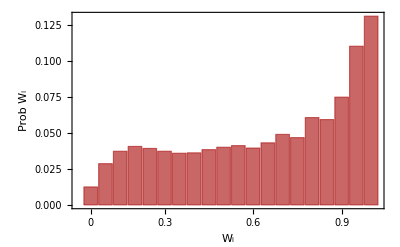

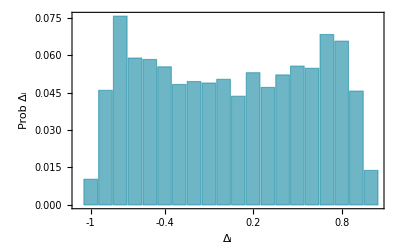

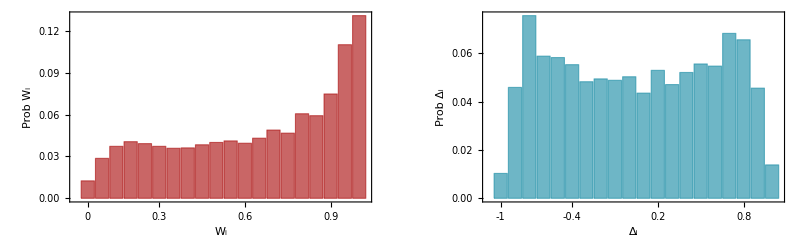

dists_combo.pdf

```mathematica
IMSC=330

WDist=Import["Wdist.csv"];
WDistHist=Import["histWVals.csv"];
WDist=Flatten[N[WDist/Total[Flatten[WDist]]]];
DDist=Import["Ddist.csv"];
DDist=Flatten[N[DDist/Total[Flatten[DDist]]]];
DDistHist=Import["histDVals.csv"];
nBins=Length[WDist]
WBar=BarChart[WDist,
ChartLabels-> {"0      ","      0.1","","      0.2","","      0.3","","      0.4","","      0.5","","      0.6","","      0.7","","      0.8","","      0.9","","      1"},
Frame-> True,
FrameLabel-> {Subscript[W, i],Prob(Subscript[W, i])},
ChartStyle-> {{colorPalette⟦2⟧},Opacity[0.6]}
]
DBar=BarChart[DDist,
ChartLabels-> {"-1      ","    -0.8","","    -0.6","","    -0.4","","     -0.2","","      0","","      0.2","","      0.4","","      0.6","","      0.8","","      1"},
Frame-> True,
FrameLabel-> {Subscript[Δ, i],Prob(Subscript[Δ, i])},
ChartStyle-> {{colorPalette⟦1⟧},Opacity[0.6]}
]
GraphicsRow[{WBar,DBar}]
Export["dists_combo.pdf",%,Rasterize-> False,ImageSize-> {900,Automatic}]
```

```mathematica
colorPalette⟦1;;5⟧
```

{RGBColor[0.0504678, 0.526626, 0.627561],RGBColor[0.65, 0., 0.],RGBColor[0.435888, 0.259065, 0.71028],RGBColor[0.752461, 0.362306, 0.125339],GrayLevel[0.5]}